```mathematica
Manipulate[Plot[(0.5*(Sin[2*Sqrt[2*a]*Sin[θ/2]]^2))/(a*(Sin[θ/2]^2)),{θ,0.0001,π-0.0001}],{a,0.1,20}]
```

```mathematica
Integrate[(0.5*(2*π*Sin[θ]*Sin[2*Sqrt[2*t]*Sin[θ/2]]^2))/(t*(Sin[θ/2]^2)),{θ,0,π},Assumptions->t>0]
```

(14.5147-6.28319 CosIntegral[4 √2 √t]+3.14159 Log[t])/t

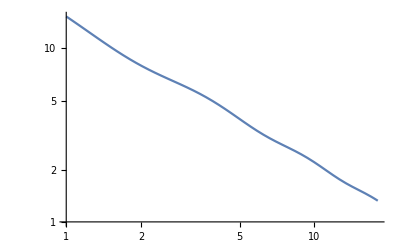

```mathematica
LogLogPlot[(14.514683436301215-6.283185307179586 CosIntegral[4 √2 √t]+3.141592653589793 Log[t])/t,{t,1.,18.}]
```

```mathematica
Export["/home/soumyananda/Dropbox/PHY622_QM/LOGLOGPLOT.png",%7,"PNG"]
```

/home/soumyananda/Dropbox/PHY622_QM/LOGLOGPLOT.png